```mathematica
Roots[x(x-1)==0,x]
```

x==1||x==0

```mathematica
Roots[Exp[I*x](x)==0,x]
```

Roots::neq: ⅇ^(ⅈ x) x is expected to be a polynomial in the variable x.

Roots[ⅇ^(ⅈ x) x==0,x]

```mathematica
Exp[0]
```

1

```mathematica
Exp[I*0]
```

1

```mathematica
Exp[I*5]
```

ⅇ^(5 ⅈ)

```mathematica
N[ⅇ^(5 ⅈ)]
```

0.283662-0.958924 ⅈ

```mathematica
Roots[-wn^2+2g*wn*I+w^2==0,wn]
```

wn==ⅈ g-√(-g^2+w^2)||wn==ⅈ g+√(-g^2+w^2)

```mathematica
C1*Exp[I*g+Sqrt[g&2+]]
```

```mathematica
Solve[-wn^2+2g*wn*I+w^2==0,wn]//Simplify
```

{{wn→ⅈ g-√(-g^2+w^2)},{wn→ⅈ g+√(-g^2+w^2)}}

```mathematica
C1=1
C2=1
k=10
g=5
```

1

1

10

5

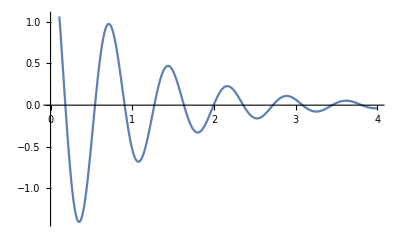

```mathematica
Plot[
Exp[-1*t]*
(C1*Exp[I*t*Sqrt[k^2-g^2]]
+C2*Exp[-I*t*Sqrt[k^2-g^2]]),{t,0,4},Background->#FFF0
]
```

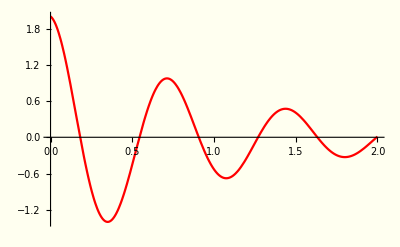

```mathematica
Plot[Exp[-t] (C1 Exp[ⅈ t √(k^2-g^2)]+C2 Exp[-ⅈ t √(k^2-g^2)]),{t,0,2},PlotTheme->"Minimal",Background->RGBColor[1.,1.,0.94117],PlotStyle->{Red}]
```

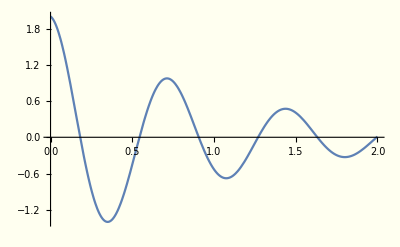

```mathematica
Show[%84,Background->RGBColor[1.,1.,0.94117]]
```

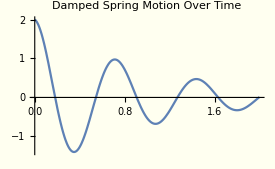

```mathematica
Show[%90,PlotLabel->HoldForm[Damped Spring Motion Over Time],Style->"Red"]
```

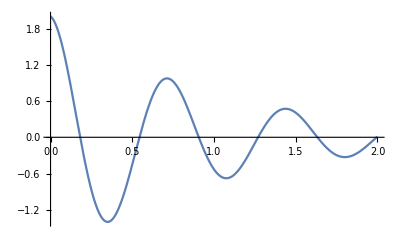

```mathematica
Show[%67,Background->RGBColor[255,255,240]]
```

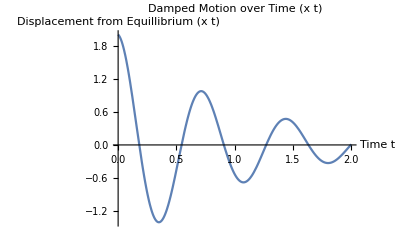

```mathematica
Show[%64,AxesLabel->{HoldForm[Time t],HoldForm[Displacement from Equillibrium (x t)]},PlotLabel->HoldForm[Damped Motion over Time (x t)],LabelStyle->{GrayLevel[0]}]
```

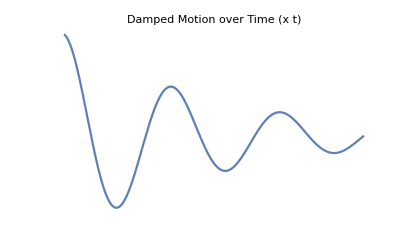

```mathematica
Show[%65,Axes->False]
```